# Title

Usage: Edit the system parameters, run the calculation cells and see the results below.
See details below. Solving the Schroedinger equation in 1D.

## Parameters

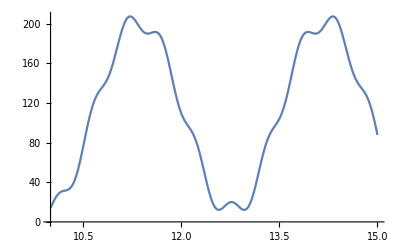

```mathematica
λ=1.064;
k=(2π)/λ;
mAtom=40  1.66 10^-27;
ℏ=1.05 10^-34;
recoilEnergyHz=(ℏ^2(k/10^-6)^2)/(2 mAtom)/(2 π ℏ);
grav=0.983; (*kHz per um*) (*not used for now*)
θxy=ArcSin[4.5/24];
potentialDepthxyErxy=100*2; (* In units of xy recoil energy. The potential depth of both X and Y lattices *)
potentialDepthxyEr=potentialDepthxyErxy Cos[θxy]^2;
potentialDepthzEr=20;
potentialEr[z_]:=potentialDepthxyEr*(1-Sin[k Sin[θxy] z]^2)+potentialDepthzEr*(1-Sin[k z]^2)
Plot[potentialEr[z],{z,10,15}]
```

## Calculations

Description of theory:

### Functions

```mathematica
findTunnelingSchroedinger[potentialFunctionEr_, xLower_, xUpper_]:=Module[{k=(2π)/1.064,x,schEq,ψSymbolic,eigenVals,eigenFuns},
schEq = -k^-2 ψSymbolic''[x]+potentialFunctionEr[x]*ψSymbolic[x];
{eigenVals,eigenFuns}=NDEigensystem[{schEq,DirichletCondition[ψSymbolic[x]==0,True]},ψSymbolic,{x,xLower,xUpper},2,Method->{"SpatialDiscretization"->{"FiniteElement",{"MeshOptions"->{MaxCellMeasure->0.001}}}}];
(eigenVals[[2]]-eigenVals[[1]])/2
];
```

```mathematica
findTunnelingFromLatticeDepths[potentialDepthzEr_,potentialDepthxyErxy_,θxy_]:=Module[{potentialDepthxyEr=potentialDepthxyErxy Cos[θxy]^2,potentialEr},potentialEr=Function[z,potentialDepthxyEr*(1-Sin[k Sin[θxy] z]^2)+potentialDepthzEr*(1-Sin[k z]^2)];
findTunnelingSchroedinger[potentialEr,11.5,14.5]];
```

## Results

```mathematica
tEr=findTunnelingSchroedinger[potentialEr,11,14];
tEr*recoilEnergyHz
```

124.594

```mathematica
findTunnelingFromLatticeDepths[15,20*2,ArcSin[4.5/24]]*recoilEnergyHz
```

110.56

```mathematica
tHzTable10=Table[{zRecoil,recoilEnergyHz*findTunnelingFromLatticeDepths[zRecoil,10*2,ArcSin[4.5/24]]},{zRecoil,3,20,0.1}];
tHzTable16=Table[{zRecoil,recoilEnergyHz*findTunnelingFromLatticeDepths[zRecoil,16*2,ArcSin[4.5/24]]},{zRecoil,3,20,0.1}];
tHzTable25=Table[{zRecoil,recoilEnergyHz*findTunnelingFromLatticeDepths[zRecoil,25*2,ArcSin[4.5/24]]},{zRecoil,3,20,0.1}];
tHzTable100=Table[{zRecoil,recoilEnergyHz*findTunnelingFromLatticeDepths[zRecoil,100*2,ArcSin[4.5/24]]},{zRecoil,3,20,0.1}];
```

```mathematica
ListLogPlot[{tHzTable10,tHzTable16,tHzTable25,tHzTable100},Joined->True,Frame->True,FrameLabel->{"Z Lattice [Er]","Tunneling matrix element, t [Hz]"},PlotLabels->{10,16,25,100},PlotLabel->"Multiple X&Y Lattice Depth",ImageSize->500, LabelStyle->16,GridLines->Automatic]
```

-Graphics-

Plot labels (the curve labels) refer to individual X & Y Lattice depths. They are both on at the same depth. Units are in recoil energy in the xy plane, approx 541 nm lattice spacing.

```mathematica
tHzTableZ10=Table[{xyRecoil,recoilEnergyHz*findTunnelingFromLatticeDepths[10,xyRecoil*2,ArcSin[4.5/24]]},{xyRecoil,3,25,0.1}];
tHzTableZ25=Table[{xyRecoil,recoilEnergyHz*findTunnelingFromLatticeDepths[25,xyRecoil*2,ArcSin[4.5/24]]},{xyRecoil,3,25,0.1}];
```

```mathematica
ListLogPlot[{tHzTableZ10,tHzTableZ25},Joined->True,Frame->True,FrameLabel->{"X&Y Lattice [Er_XY]","Tunneling matrix element, t [Hz]"},PlotLabels->{10,25},PlotLabel->"Multiple Z Lattice Depth",ImageSize->500, LabelStyle->16,GridLines->Automatic]
```

-Graphics-

X axis label refers to individual X & Y Lattice depths. They are both on at the same depth. Units are in recoil energy in the xy plane, approx 541 nm lattice spacing.